# Limit

## Function

```mathematica
f[x_]=SquareWave[x](x-1);
```

Point

```mathematica
a=1/2;
```

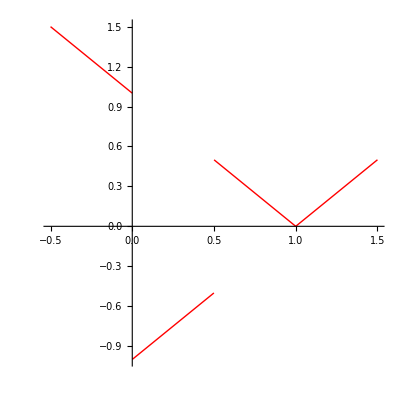

```mathematica
Plot[f[x],{x,a-1,a+1},PlotStyle->{Red,Thick},AspectRatio->1]
```

```mathematica
f[a]
```

1/2

## Limits from the left :

```mathematica
Table[{x,f[x]},{x,{a-0.1,a-0.01,a-0.001,a-0.0001,a-0.00001}}]//TableForm
```

0.4 | -0.6
0.49 | -0.51
0.499 | -0.501
0.4999 | -0.5001
0.49999 | -0.50001

```mathematica
Limit[f[x],x->a,Direction->1]
```

-1/2

## Limits from the right:

```mathematica
Table[{x,f[x]},{x,{a+0.1,a+0.01,a+0.001,a+0.0001,a+0.00001}}]//TableForm
```

0.6 | 0.4
0.51 | 0.49
0.501 | 0.499
0.5001 | 0.4999
0.50001 | 0.49999

```mathematica
Limit[f[x],x->a,Direction->-1]
```

1/2